## 1.Naloga

```mathematica
d = Daljica[{-1,1},{3,-1}]
d2= Daljica[{-1,-1},{3,1}]
d3= Daljica[{-1,2},{3,0}]
```

Daljica[{-1,1},{3,-1}]

Daljica[{-1,-1},{3,1}]

Daljica[{-1,2},{3,0}]

```mathematica
Dolzina[Daljica[AA_,BB_]]:= Norm[BB - AA]
```

```mathematica
Dolzina[d2]
```

2 √5

```mathematica
Slika[Daljica[AA_,BB_]]:=Line[{AA,BB}]
```

```mathematica
Slika[d]
```

Line[{{-1,1},{3,-1}}]

```mathematica
Narisi[d_Daljica]:= Graphics[Slika[d]]
```

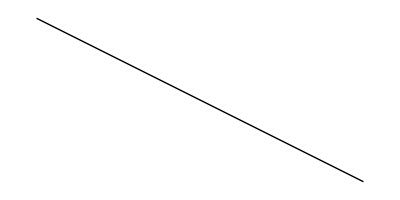

```mathematica
Narisi[d]
```

```mathematica
EnacbaNosilke[Daljica[AA_,BB_]]:= Module[{x1,y1,x2,y2,k,n},
{x1,y1}=AA;
{x2,y2}=BB;
k =(y2-y1)/(x2-x1);
n = n /. First[Solve[y1==k*x1+n,n]];
y = k*x + n
]
```

```mathematica
EnacbaNosilke[d]
```

1/2-x/2

## 2.Naloga

```mathematica
Presek[Daljica[AA_,BB_],Daljica[CC_,DD_]]:= Module[{resitev},
resitev = Solve[{AA+r(BB-AA) == CC+s(DD-CC),r≥0,r≤1,s≥ 0,s≤1},{r,s}];
If[resitev=={},
{},
First[AA+r(BB-AA)/.resitev]
]]
```

```mathematica
Presek[d,d3]
```

{}

## 3.Naloga

```mathematica
m1 = Mnogokotnik[{0,0},{1,1},{0,3},{-1,2}]
m2 = Append[m1,First[m1]]
```

Mnogokotnik[{0,0},{1,1},{0,3},{-1,2}]

Mnogokotnik[{0,0},{1,1},{0,3},{-1,2},{0,0}]

```mathematica
Slika[Mnogokotnik[t__]]:=Line[Append[{t},First[{t}]]]
```

```mathematica
Narisi[m__Mnogokotnik]:=Graphics[Slika[m]]
```

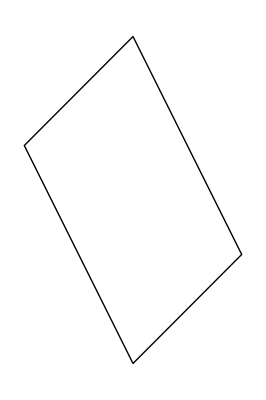

```mathematica
Narisi[m1]
```

```mathematica
PravilniNKotnik[n_,r_]:=Graphics[
{Line
[Table[{r*Cos[(2Pi*i)/n],r*Sin[(2Pi*i)/n]},{i,0,n}]],
Point[{0,0}]
}
]
```

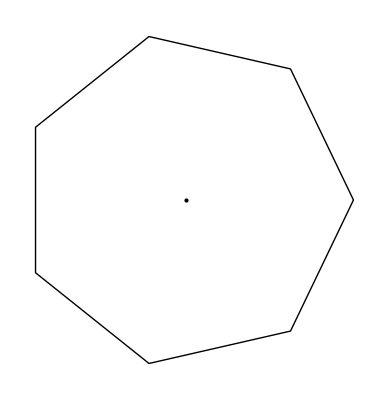

```mathematica
p5=PravilniNKotnik[7,2]
```

```mathematica
PravilniNKotnik[n_,r_,phi_]:=Manipulate[Graphics[{Line[{Table[{r* Cos[(2*Pi * i+phi)/n],r*Sin[(2 Pi *i+phi)/n]},{i,0,n}]}],Point[ {0,0}]}]
,{phi,2,20}]
```

```mathematica
PravilniNKotnik[10,3,phi]
```

## 4.Naloga

```mathematica
Presek2[m_Mnogokotnik,d_Daljica] := Presek[daljice[[1]],d]
```

## 5.Naloga

```mathematica
VsiPari[f_,sez1_,sez2_]:=Flatten[Outer[f,sez1,sez2],1]
VsiPari[f,{1,2,3},{a,b}]
```

{f[1,a],f[1,b],f[2,a],f[2,b],f[3,a],f[3,b]}

```mathematica
VsiPari[k,{2,3,4},{7,3,5}]
```

{k[2,7],k[2,3],k[2,5],k[3,7],k[3,3],k[3,5],k[4,7],k[4,3],k[4,5]}

```mathematica
VsiPari[f,{{1,2},{3,4}},{{aa,bb},{dd,cc}}]
```

{{{f[1,aa],f[1,bb]},{f[1,dd],f[1,cc]}},{{f[2,aa],f[2,bb]},{f[2,dd],f[2,cc]}},{{f[3,aa],f[3,bb]},{f[3,dd],f[3,cc]}},{{f[4,aa],f[4,bb]},{f[4,dd],f[4,cc]}}}

```mathematica
Outer[f,{2,4,3,{5},9}]
```

{f[2],f[4],f[3],{f[5]},f[9]}

```mathematica
Flatten[Outer[f,{2,4,3,{5},9}],1]
```

```mathematica
{f[2],f[4],f[3],f[5],f[9]}
```

## 6.Naloga

```mathematica
Premica[A_,B_]:=Numerator[Ploščina[A,B,{x,y}]]==0
```

```mathematica
Premica[{0,1},{1,3}]
```

Ploščina[{0,1},{1,3},{x,1/2-x/2}]==0

```mathematica
Premica[A_,B_]:=Numerator[Ploščina[A,B,{x,y}]]==0/.Abs->Identity
```

```mathematica
Premica[{0,1},{1,3}]
```

Ploščina[{0,1},{1,3},{x,1/2-x/2}]==0